## 7강 선형대수학

전경원 <ruddyscent@gmail.com>

2014년 11월 3일 월요일

```mathematica
$Version
DateString[]
```

10.0 for Linux x86 (64-bit) (September 9, 2014)

Mon 3 Nov 2014 14:11:27

## 행렬

### 행렬의 입력

매스매티카는 행렬을 표현하는데, 중첩 리스트를 사용합니다.

```mathematica
mat1=({{2, 3, 4, 5, 6, 7}, {1, 1, 1, 1, 1, 1}, {4, 5, 4, 5, 4, 5}, {11, 2, 2, 2, 2, 2}, {0, 0, 0, 0, 0, 1}})
```

{{2,3,4,5,6,7},{1,1,1,1,1,1},{4,5,4,5,4,5},{11,2,2,2,2,2},{0,0,0,0,0,1}}

```mathematica
mat2={{1,2,3},{3,4,5},{5,6,7}}
```

{{1,2,3},{3,4,5},{5,6,7}}

모양이 좀 그렇죠. 행렬처럼 보이게 하려면,  MatrixForm을 써보세요.

```mathematica
mat2//MatrixForm
```

(1 | 2 | 3
3 | 4 | 5
5 | 6 | 7)

행렬의 크기를 알고 싶다면, Dimensions를 써보세요.

```mathematica
Dimensions[mat1]
```

{5,6}

0에서 50 사이의 무작위 정수로 이루어진 3x5 행렬을 만들자면,

```mathematica
RandomInteger[50,{3,5}]//MatrixForm
```

(4 | 9 | 7 | 28 | 19
0 | 4 | 35 | 44 | 30
21 | 26 | 43 | 26 | 11)

i행 j열이 i+2j로 이루어진 5x5 행렬을 만들어 볼까요?

```mathematica
Table[i+2j,{i,5},{j,5}]//MatrixForm
```

(3 | 5 | 7 | 9 | 11
4 | 6 | 8 | 10 | 12
5 | 7 | 9 | 11 | 13
6 | 8 | 10 | 12 | 14
7 | 9 | 11 | 13 | 15)

반복자의 시작값을 정할 수도 있어요.

```mathematica
Table[i+2j,{i,-2,3},{j,0,2}]//MatrixForm
```

(-2 | 0 | 2
-1 | 1 | 3
0 | 2 | 4
1 | 3 | 5
2 | 4 | 6
3 | 5 | 7)

3x4짜리 0 행렬이 필요하다면,

```mathematica
Table[0,{3},{4}]//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

상수 행렬을 만드는 일을 전문적으로 하는 명령도 있답니다.

```mathematica
ConstantArray[0,{3,5}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0)

조건식을 이용하여 행렬에 특별한 구조를 부여할 수도 있지요.

```mathematica
Table[If[i≥j,i+2j,0],{i,4},{j,4}]//MatrixForm
```

(3 | 0 | 0 | 0
4 | 6 | 0 | 0
5 | 7 | 9 | 0
6 | 8 | 10 | 12)

Array 명령은 Table과 비슷하긴 하지만, 원소 표현에 함수를 이용할 수 있다는 차이점이 있습니다.

```mathematica
Array[Min,{4,5}]//MatrixForm
```

(1 | 1 | 1 | 1 | 1
1 | 2 | 2 | 2 | 2
1 | 2 | 3 | 3 | 3
1 | 2 | 3 | 4 | 4)

```mathematica
Clear[f];
f[i_,j_]:=i^3+j^2
Array[f,{2,3}]//MatrixForm
```

(2 | 5 | 10
9 | 12 | 17)

Array를 이용하면 쉽게 행렬의 일반형을 만들 수 있습니다.

```mathematica
Clear[a,mat];
mat=Array[Subscript[a, ##]&,{3,4}];mat//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4))

다음 명령은 단위행렬을 만듭니다.

```mathematica
IdentityMatrix[4]//MatrixForm
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

DiagonalMatrix는 주어진 원소를 원소로 하는 대각행렬을 만듭니다.

```mathematica
DiagonalMatrix[{a,b,c,d}]//MatrixForm
```

(a | 0 | 0 | 0
0 | b | 0 | 0
0 | 0 | c | 0
0 | 0 | 0 | d)

```mathematica
DiagonalMatrix[{a,b,c},1]//MatrixForm
```

(0 | a | 0 | 0
0 | 0 | b | 0
0 | 0 | 0 | c
0 | 0 | 0 | 0)

```mathematica
DiagonalMatrix[{a,b,c},-1]//MatrixForm
```

(0 | 0 | 0 | 0
a | 0 | 0 | 0
0 | b | 0 | 0
0 | 0 | c | 0)

### 행렬의 변형

ArrayFlatten을 이용하면, 행렬을 통째로 다른 행렬 안에 넣을 수 있습니다.

```mathematica
mat1=RandomInteger[9,{3,4}];
mat1//MatrixForm
```

(9 | 1 | 3 | 9
5 | 4 | 4 | 3
3 | 3 | 1 | 6)

```mathematica
mat2=RandomInteger[9,{3,4}];
mat2//MatrixForm
```

(6 | 1 | 6 | 9
7 | 6 | 7 | 7
9 | 9 | 9 | 1)

열 맞추기

```mathematica
ArrayFlatten[{{mat1},{mat2}}]//MatrixForm
```

(0 | 7 | 4 | 3
1 | 7 | 5 | 8
2 | 4 | 7 | 1
6 | 1 | 6 | 9
7 | 6 | 7 | 7
9 | 9 | 9 | 1)

행 맞추기

```mathematica
ArrayFlatten[{{mat1,mat2}}]//MatrixForm
```

(0 | 7 | 4 | 3 | 6 | 1 | 6 | 9
1 | 7 | 5 | 8 | 7 | 6 | 7 | 7
2 | 4 | 7 | 1 | 9 | 9 | 9 | 1)

나머지 부분은 손쉽게 상수로 채울 수도 있습니다.

```mathematica
bm=ArrayFlatten[{{mat1,0},{0,mat2}}];
bm//MatrixForm
```

(0 | 7 | 4 | 3 | 0 | 0 | 0 | 0
1 | 7 | 5 | 8 | 0 | 0 | 0 | 0
2 | 4 | 7 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 6 | 1 | 6 | 9
0 | 0 | 0 | 0 | 7 | 6 | 7 | 7
0 | 0 | 0 | 0 | 9 | 9 | 9 | 1)

Take로 행렬의 일부를 빼내 볼까요?

```mathematica
Clear[a,mat];
mat=Array[Subscript[a, ##]&,{5,5}];
mat//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5)
a_(5,1) | a_(5,2) | a_(5,3) | a_(5,4) | a_(5,5))

```mathematica
Take[mat,3]//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5))

```mathematica
Take[mat,-2]//MatrixForm
```

(a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5)
a_(5,1) | a_(5,2) | a_(5,3) | a_(5,4) | a_(5,5))

```mathematica
Take[mat,{2,4}]//MatrixForm
```

(a_(2,1) | a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5)
a_(4,1) | a_(4,2) | a_(4,3) | a_(4,4) | a_(4,5))

```mathematica
Take[mat,{1,-1,2}]//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(3,1) | a_(3,2) | a_(3,3) | a_(3,4) | a_(3,5)
a_(5,1) | a_(5,2) | a_(5,3) | a_(5,4) | a_(5,5))

```mathematica
Take[mat,2,-4]//MatrixForm
```

(a_(1,2) | a_(1,3) | a_(1,4) | a_(1,5)
a_(2,2) | a_(2,3) | a_(2,4) | a_(2,5))

```mathematica
Take[mat,All,-3]//MatrixForm
```

(a_(1,3) | a_(1,4) | a_(1,5)
a_(2,3) | a_(2,4) | a_(2,5)
a_(3,3) | a_(3,4) | a_(3,5)
a_(4,3) | a_(4,4) | a_(4,5)
a_(5,3) | a_(5,4) | a_(5,5))

```mathematica
Take[mat,{2,4},{3,5}]//MatrixForm
```

(a_(2,3) | a_(2,4) | a_(2,5)
a_(3,3) | a_(3,4) | a_(3,5)
a_(4,3) | a_(4,4) | a_(4,5))

```mathematica
Take[mat,{1,4,3},{2,4,2}]//MatrixForm
```

(a_(1,2) | a_(1,4)
a_(4,2) | a_(4,4))

```mathematica
mat⟦1;;4;;3,2;;4;;2⟧//MatrixForm
```

(a_(1,2) | a_(1,4)
a_(4,2) | a_(4,4))

행렬의 일부를 지칭하려면 "[[]]"를 이용합니다.

```mathematica
mat1=({{0, 7, 4, 3}, {1, 7, 5, 8}, {2, 4, 7, 1}})//MatrixForm
```

(0 | 7 | 4 | 3
1 | 7 | 5 | 8
2 | 4 | 7 | 1)

```mathematica
mat1⟦2⟧
```

{1,7,5,8}

```mathematica
mat1_⟦2⟧
```

{1,7,5,8}

```mathematica
mat1_⟦3,4⟧
```

1

```mathematica
mat1_⟦All,3⟧
```

{4,5,7}

## 행렬의 연산

두 행렬의 차원이 같다면 다음과 같이 더할 수 있답니다.

```mathematica
mat3=({{1, 0, 0}, {2, 3, 4}, {-1, 5, -1}});
mat4=({{2, 2, 3}, {0, 0, 1}, {5, 5, 5}});
mat3+mat4//MatrixForm
```

(3 | 2 | 3
2 | 3 | 5
4 | 10 | 4)

뺄 수도 있어요.

```mathematica
mat3-mat4//MatrixForm
```

(-1 | -2 | -3
2 | 3 | 3
-6 | 0 | -6)

상수를 곱할수도 있어요.

```mathematica
7*mat3
```

(7 | 0 | 0
14 | 21 | 28
-7 | 35 | -7)

행렬곱은 조금 복잡합니다.

```mathematica
mat3.mat4//MatrixForm
```

(2 | 2 | 3
24 | 24 | 29
-7 | -7 | -3)

‘*’는 행렬을 곱하는 게  아니라 원소끼리 곱합니다.

```mathematica
mat3 *mat4//MatrixForm
```

(2 | 0 | 0
0 | 0 | 4
-5 | 25 | -5)

한 행렬을 여러번 곱하려면 MatrixPower를 이용하세요.

```mathematica
MatrixPower[mat3,10]//MatrixForm
```

(1 | 0 | 0
10249364 | 36166989 | 20498728
7834130 | 25623410 | 15668261)

Transpose는 전치행렬을 구하는데 사용합니다.

```mathematica
Transpose[mat3]//MatrixForm
```

(1 | 2 | -1
0 | 3 | 5
0 | 4 | -1)

역행렬이 존재한다면, Inverse로 구할 수 있습니다.

```mathematica
Inverse[mat3]//MatrixForm
```

(1 | 0 | 0
2/23 | 1/23 | 4/23
-13/23 | 5/23 | -3/23)

```mathematica
Inverse[mat3].mat3//MatrixForm
```

(1 | 0 | 0
0 | 1 | 0
0 | 0 | 1)

행렬식은 역행렬이 존재한다면, 0이 아닌 수를 반환하는 식입니다.

```mathematica
Det[mat3]
```

-23

```mathematica
Clear[a]
mat5=Array[Subscript[a, ##]&,{3,3}];
mat5//MatrixForm
```

(a_(1,1) | a_(1,2) | a_(1,3)
a_(2,1) | a_(2,2) | a_(2,3)
a_(3,1) | a_(3,2) | a_(3,3))

```mathematica
Det[mat5]
```

-a_(1,3) a_(2,2) a_(3,1)+a_(1,2) a_(2,3) a_(3,1)+a_(1,3) a_(2,1) a_(3,2)-a_(1,1) a_(2,3) a_(3,2)-a_(1,2) a_(2,1) a_(3,3)+a_(1,1) a_(2,2) a_(3,3)

행렬식이 역행렬의 어느 부분에 들어가닌지 확인해 보면, 행렬식의 의미를 파악할 수 있습니다.

```mathematica
Inverse[mat5]⟦1,1⟧
```

(-a_(2,3) a_(3,2)+a_(2,2) a_(3,3))/(-a_(1,3) a_(2,2) a_(3,1)+a_(1,2) a_(2,3) a_(3,1)+a_(1,3) a_(2,1) a_(3,2)-a_(1,1) a_(2,3) a_(3,2)-a_(1,2) a_(2,1) a_(3,3)+a_(1,1) a_(2,2) a_(3,3))

```mathematica
Inverse[mat5]⟦1,1⟧/.Det[mat5]->det
```

(-a_(2,3) a_(3,2)+a_(2,2) a_(3,3))/det

행렬의 대각합은 Tr로 구합니다.

```mathematica
Tr[mat5]
```

a_(1,1)+a_(2,2)+a_(3,3)

## 가우스 소거법

RowReduced를 이용하면 손쉽게 가우스 소거법을 수행할 수 있습니다.

```mathematica
Clear[mat];
mat=({{1, 1, 4, 25}, {2, 1, 0, 7}, {-3, 0, 1, -1}});
RowReduce[mat]//MatrixForm
```

(1 | 0 | 0 | 2
0 | 1 | 0 | 3
0 | 0 | 1 | 5)

물론 이 과정을 직접 일일이 해볼 수도 있겠죠.

```mathematica
mat⟦2⟧=mat⟦2⟧-2mat⟦1⟧;
mat//MatrixForm
```

(1 | 1 | 4 | 25
0 | -1 | -8 | -43
-3 | 0 | 1 | -1)

```mathematica
mat⟦3⟧=mat⟦3⟧+3mat⟦1⟧;
mat⟦1⟧=mat⟦1⟧+mat⟦2⟧;
mat//MatrixForm
```

(1 | 0 | -4 | -18
0 | -1 | -8 | -43
0 | 3 | 13 | 74)

```mathematica
mat⟦3⟧=mat⟦3⟧+3mat⟦2⟧;
mat//MatrixForm
```

(1 | 0 | -4 | -18
0 | -1 | -8 | -43
0 | 0 | -11 | -55)

```mathematica
mat⟦3⟧=-1/11 mat⟦3⟧;
mat⟦2⟧=-mat⟦2⟧;
mat⟦2⟧=mat⟦2⟧-8mat⟦3⟧;
mat⟦1⟧=mat⟦1⟧+4mat⟦3⟧;
mat//MatrixForm
```

(1 | 0 | 0 | 2
0 | 1 | 0 | 3
0 | 0 | 1 | 5)

## 선형 방정식의 풀이

최고차항의 차수가 1인 방정식을 행렬을 이용하여 풀어보겠습니다.

다음 세 점을 포함하는 원의 방정식을 찾아보자: (4,-3), (-4,5), (-2,7).

```mathematica
Clear[eq,a,b,c,d,m]
eq=a x^2+a y^2+b x +c y + d==0;
```

```mathematica
eq/.{{x->4,y->-3},{x->-4,y->5},{x->-2,y->7}}
{bb,mm}=CoefficientArrays[%,{a,b,c,d}]//Normal
```

{25 a+4 b-3 c+d==0,41 a-4 b+5 c+d==0,53 a-2 b+7 c+d==0}

{{0,0,0},{{25,4,-3,1},{41,-4,5,1},{53,-2,7,1}}}

```mathematica
mm//RowReduce//MatrixForm
```

(1 | 0 | 0 | 1/29
0 | 1 | 0 | -2/29
0 | 0 | 1 | -4/29)

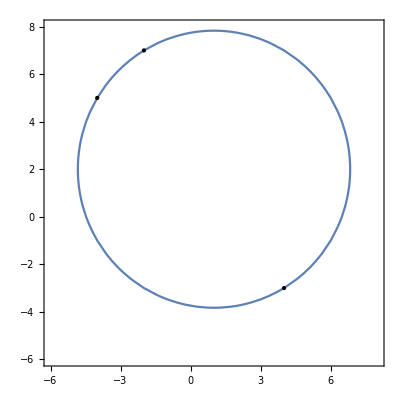

```mathematica
ContourPlot[Evaluate@(eq/.{a->-1,b->2,c->4,d->29}),{x,-6,8},{y,-6,8},Epilog->Point[{{4,-3},{-4,5},{-2,7}}]]
```

## 선형 변환의 예

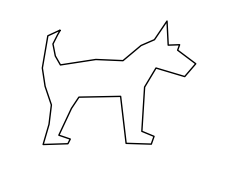

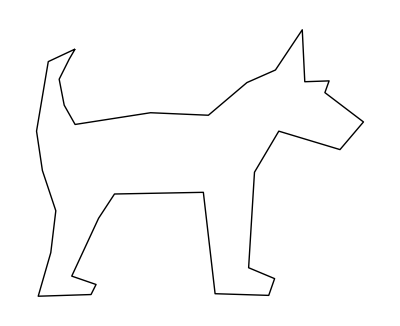
```mathematica
dog=First@Cases[-Graphics-,Line[pts_]->pts,Infinity]
```

{{0.277778,0.897222},{0.188889,0.855556},{0.15,0.625},{0.169444,0.494444},{0.213889,0.361111},{0.197222,0.222222},{0.155556,0.0777778},{0.330556,0.0833333},{0.347222,0.116667},{0.266667,0.144444},{0.355556,0.336111},{0.408333,0.416667},{0.702778,0.422222},{0.741667,0.0861111},{0.919444,0.0805556},{0.938889,0.136111},{0.852778,0.172222},{0.872222,0.488889},{0.952778,0.625},{1.15556,0.563889},{1.23333,0.655556},{1.10556,0.752778},{1.11944,0.791667},{1.03889,0.788889},{1.03056,0.961111},{0.941667,0.827778},{0.847222,0.786111},{0.719444,0.677778},{0.527778,0.686111},{0.277778,0.647222},{0.241667,0.711111},{0.225,0.797222},{0.258333,0.863889},{0.277778,0.897222}}

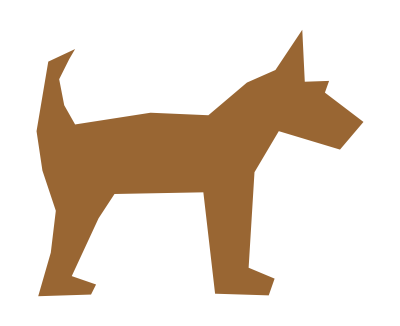
{-Graphics-,-Graphics-}

```mathematica
{Graphics@Line@dog,Graphics@{Brown,Polygon@dog}}
```

강아지를 y 축에 대해 대칭 변환해 볼까요?

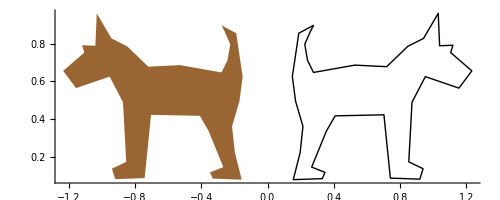

```mathematica
Graphics[{{Brown,Polygon@Table[({{-1, 0}, {0, 1}}).v,{v,dog}]},Line@dog},Axes->True]
```

이번엔 선분 y=x에 대해 대칭 변환해 봅시다.

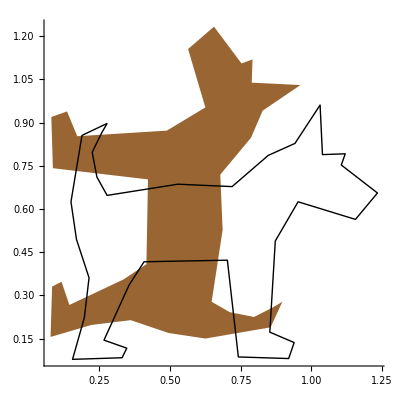

```mathematica
Graphics[{{Brown,Polygon@Table[({{0, 1}, {1, 0}}).v,{v,dog}]},Line@dog},Axes->True]
```